```mathematica
<<Units`
ppgfttoPSI=0.0519481;
```

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
pt1[[1]]+(y-pt1[[2]])(pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]])
];

Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]≤Abs[ycoord]≤ Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord];
];
];
];
```

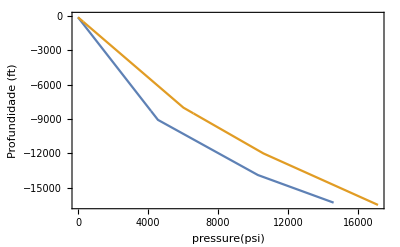

```mathematica
dataporepressure={{8.33,-100},{9.7,-9066},{14.25,-13885},{17.25,-16300}};
PtsFracPressure={{9,-100},{14.5,-6025.97},{17,-12000},{20,-16500}};
dataporepressure={{0,-100},{4568.32,-9066},{10278.50,-13885},{14606.48,-16300}};
PtsFracPressure={{0,-100},{6025.97,-8000},{10597.39,-12000},{17142.84,-16500}};
tabpore=Table[{Interpolate[y,dataporepressure],y},{y,-16300,0}];
tabfrac=Table[{Interpolate[y,PtsFracPressure],y},{y,-16500,0}];
ListLinePlot[{tabpore,tabfrac},Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"pressure(psi)"," Janela Operacional "}},LabelStyle->Directive[Bold,14],Axes->None]
```

```mathematica
MakeCompatibleSizeVectors[refinedvec_,coarsevecl_,coarsevecvar_]:=Block[{newvec,y0,y1,x0,x1,counter,i},
newvec={};
counter=1;
If[Length[coarsevecl]!=Length[coarsevecvar],
Print["Não é possível realizar o refinamento, os vetores coarse devem ter o mesmo tamanho."];
];
For[i=1,i<Length[coarsevecl],i++,
(*If[i>=Length[coarsevecvar],Break[]];*)
y0=coarsevecvar[[i]];
y1=coarsevecvar[[i+1]];
x0=coarsevecl[[i]];
x1=coarsevecl[[i+1]];
While[(coarsevecl[[i]]<=refinedvec[[counter]]<=coarsevecl[[i+1]])&&counter<Length[refinedvec],
AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]];
counter++;
];
If[i==Length[coarsevecl]-1,AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]]];
];
newvec//N
]
```

```mathematica
(*refina de n divisões de refl até lf*)
refine[l0_,lf_,refl_,n_,nreffull_]:=Block[{dref,standardref=nreffull,refinedvec,lastcoarsedata,i},
refinedvec=Table[dl//N,{dl,l0,refl,(refl-l0)/standardref}];
lastcoarsedata=refl;
If[Abs[lf-refl]<10^-8,
dref=(lf-l0)/n;
refinedvec={};
lastcoarsedata=l0;
,
dref=(lf-refl)/n;
lastcoarsedata=refl;
];

For[i=1,i≤n,i++,
AppendTo[refinedvec,lastcoarsedata//N];
lastcoarsedata+=dref;
];
AppendTo[refinedvec,N[lf]];
refinedvec//N
]
```

```mathematica
L0=0.;
LF=14800.;
LtoRef=14799;
nrefs=50.;
refinedl=refine[L0,LF,LtoRef,nrefs];
```

```mathematica
refinedl
```

refine[0.,14800.,14799,50.]

```mathematica
Length[refinedl]
```

4

Dado PI e PO, rint e rext, faz o cálculo da tensão radial e tangencial

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}//N
];
ComputeRadialAndTangetialStress2[r_,ri_,re_,PI_,PO_,FZ_]:=Block[{ez,sigrr,sigtt,sigzz,a,b,Pa,Pb,nu=0.30,young=3 10^7},
a=ri;
b=re;
Pa=PI;
Pb=PO;
ez=FZ/(Pi young(b^2-a^2))-(2nu)/young(Pa a^2 -Pb b^2)/(b^2-a^2);
sigrr=(Pa a^2 -Pb b^2)/(b^2-a^2)-(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigtt=(Pa a^2 -Pb b^2)/(b^2-a^2)+(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigzz=2 nu (Pa a^2 -Pb b^2)/(b^2-a^2)+young ez;
{sigrr,sigtt,sigzz}//N
];
(*di=12.376;
de=14;
{sigr,sigt,sigz}=ComputeRadialAndTangetialStress2[di/2 ,di/2,de/2,8237,3629,1.312705856587157*^6]
sigz Pi/4( de^2-di^2)*)
```

Dado dint, dext, PI e PO, faz o cálculo da tensão axial (TA) devido ao efeito poisson (Balão)

```mathematica
ComputeFballoning[di_,de_,Pint_,Pext_,nu_]:=Block[{sigr,sigt,Fballoning},
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,Pint,Pext];
Fballoning=nu(sigr+sigt)Pi/4( de^2-di^2);
Fballoning//N
];
```

```mathematica
ComputeFtemperature[de_,di_,TM_,TPM_]:=Block[{young = 3 10^7,alfa=6.9 10^-6,ΔT,T1,f,fp,T2,Ftemperature},
ΔT= (TPM-TM) ;
Ftemperature=-young alfa ΔT Pi/4(de^2-di^2);
Ftemperature//N
]
```

```mathematica
ComputeFBend[de_,di_,θ_]:=Block[{young = 3. 10^7,area,Fbend},
area=Pi/4. (de^2. -di^2.);
Fbend=Pi young de θ/(100. 360. 12.) area;
Fbend//N(*resultado em lb*)
]
```

```mathematica
di=19.124;
de=20;
ComputeFBend[de,di,2]
```

234901.

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i≥1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum;(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_,doglegdata_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i≥1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum+ComputeFBend[de,di,doglegdata[[i]]];(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_]:=Block[{Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
Print["Length[InternalPressKick] = ",Length[InternalPressKick]];
Print["Length[InternalPressinitial] = ",Length[InternalPressinitial]];
Print["Length[ExternalPressKick] = ",Length[ExternalPressKick]];
Print["Length[ExternalPressinitial] = ",Length[ExternalPressinitial]];
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i≥1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];
{Fi,Ffinal}//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_,doglegdata_]:=Block[{Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData,doglegdata];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
Print["Length[InternalPressKick] = ",Length[InternalPressKick]];
Print["Length[InternalPressinitial] = ",Length[InternalPressinitial]];
Print["Length[ExternalPressKick] = ",Length[ExternalPressKick]];
Print["Length[ExternalPressinitial] = ",Length[ExternalPressinitial]];
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i≥1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];
{Fi,Ffinal}//N
]
```

Calcula a resistência do tubular à ruptura e ao colapso de acordo com a API BUL 5C3

```mathematica
ComputePipeStrength[siga_,sigy_,de_,di_,young_,nu_]:=Block[{t=(de-di)/2,BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(de/t);
dt=de/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);

If[dt≥ range1,

ColapseStrength=(2 young)/(1-nu^2) 1/(dt(dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2≤ dt≤ range1,

ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3≤ dt≤ range2),

ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt≤ range3,

ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}//N
];
```

Calcula a tensão de von Mises

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2,vm,teste},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};

S=sig-1/3 Tr[sig] IdentityMatrix[3];
J2=1/2 Tr[S.S];
Sqrt[3 J2]
];
```

```mathematica
ComputeVonMises[sigr,sigt,siga]
```

√(3/2) √((siga+1/3 (-siga-sigr-sigt))^2+(sigr+1/3 (-siga-sigr-sigt))^2+(1/3 (-siga-sigr-sigt)+sigt)^2)

```mathematica
√(3/2) √((siga+1/3 (-siga-sigr-sigt))^2+(sigr+1/3 (-siga-sigr-sigt))^2+(1/3 (-siga-sigr-sigt)+sigt)^2)//Simplify
```

√(siga^2+sigr^2-sigr sigt+sigt^2-siga (sigr+sigt))

1.3 Pressão resistente de Klever Stewart

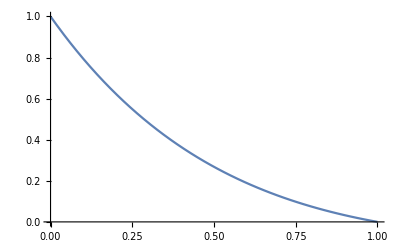

```mathematica
Plot[-3^(1-n)+4^(1-n),{n,0,1}]
```

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{a,kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n));
If[sa<fu,a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)),a=(1-fu^2/fu^2)/(-3^(1-n)+4^(1-n))];
pfactorNeck=Sqrt[a];
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
If[sa/fu≤ ((√3)/2)^(1-n),
If[pM≤ (pM+0.5^n puts)/2,
pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
];
pburst//N
];
```

```mathematica
(*ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
pBurstKS

];*)
```

1.3 Pressão resistente de Klever Tamano

Calcula os fatores de segurança

```mathematica
ComputeSafetyFactors[PipeData_,AxialForce_,Pint_,Pext_,ov_,ec_,rs_]:=Block[{KTStress,KSstress,KSSF={},KTSF={},APISF={}, BarlowSF={},i,barlow,api,de,di,young,nu,weigthperfeet,L1,L2,pipe=1,sigy,VMSF={},sigr,sigt,area,VMStress},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
For[i=Length[Pint]-1,i>1,i--,
If[L1>Pint[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
];
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,Pint[[i,1]],Pext[[i,1]]];
area=Pi/4 (de^2 -di^2);


VMStress=ComputeVonMises[sigr,sigt,AxialForce[[i,1]]/area];
KSstress=ComputeBurstResistance[1,de,0.5(de -di),sigy,AxialForce[[i,1]]/area,Pext[[i,1]]];
KTStress=ComputeColapseStrengthKT[AxialForce[[i,1]]/area,sigy,Pint[[i,1]],de,0.5(de -di),young,nu,ov,ec,rs];
api=ComputePipeStrength[AxialForce[[i,1]]/area,sigy,de,di,young,nu];
If[burst==True,
deltap=(Pint[[i,1]]-Pext[[i,1]]);
,
deltap=(-Pint[[i,1]]+Pext[[i,1]]);
];
AppendTo[BarlowSF,{api[[1]]/deltap,-Pint[[i,2]]}];
AppendTo[APISF,{api[[2]]/deltap,-Pint[[i,2]]}];
AppendTo[VMSF,{sigy/VMStress,-Pint[[i,2]]}];
AppendTo[KSSF,{KSstress/deltap,-Pint[[i,2]]}];
AppendTo[KTSF,{KTStress/deltap,-Pint[[i,2]]}];
];
{BarlowSF,APISF,VMSF,KSSF,KTSF}
];
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{ke=1,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs,sigy];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

# MUD DROP DUE TO LOST RETURNS

# -Graphics-

```mathematica
burst=False;
lvec={0,100,951,1901,2100,2100,2581,2851,2995,3409,3801,3823,4237,4651,4751,5065,5479,5700,5893,6307,6650,6721,7135,7549,7600,7963,8377,8550,8791,9066,9205,9500,9500,9618,9700,9700,9950,10032,10400,10446,10850,10860,11274,11300,11688,11750,12102,12200,12516,12650,12930,13100,13344,13550,13758,13885,14000,14100,14172,14200,14300,14400,14500,14586,14600,14700,14800,14900,15000};
InternalPressLostCirc={1.36,1.36,1.36,1.37,1.37,1.37,1.37,246.55,377.70,754.03,1110.09,1130.36,1506.70,1883.03,1973.64,2259.36,2635.70,2837.18,3012.03,3388.36,3700.72,3764.69,4141.03,4517.36,4564.27,4893.69,5270.03,5427.82,5646.36,5896.81,6022.69,6291.27,6291.45,6399.03,6473.09,6473.27,6700.45,6775.36,7109.54,7151.69,7518.63,7528.02,7904.36,7927.72,8280.69,8336.81,8657.02,8745.90,9033.36,9154.99,9409.69,9564.08,9786.02,9973.17,10162.35,10277.71,10382.26,10473.17,10538.69,10564.08,10654.99,10745.90,10836.81,10915.02,10927.72,11018.63,11109.53,11200.44,11291.26};
ExternalPressLostCirc={0.00,74.49,715.43,1430.94,1580.91,1581.06,1943.30,2146.45,2255.12,2566.93,2861.96,2878.76,3190.58,3502.39,3577.47,3814.21,4126.04,4292.98,4437.85,4749.67,5008.49,5061.49,5373.31,5685.13,5724.00,5996.95,6308.76,6439.51,6620.59,6828.10,6932.40,7154.94,7155.92,7245.04,7306.41,7306.57,7494.80,7556.87,7833.76,7868.69,8172.72,8180.50,8492.32,8511.68,8804.15,8850.64,9115.96,9189.60,9427.78,9528.56,9739.60,9867.52,10051.41,10206.48,10363.23,10458.82,10545.44,10620.77,10675.05,10696.09,10771.42,10846.74,10922.07,10986.87,10997.39,11072.72,11148.04,11223.37,11298.62};
AxialForceLostCircWellCat={572652,567361,521838,471018,460366,460355,434627,420198,412480,390333,369379,368186,346038,323891,318559,301744,279597,267739,257450,235302,216920,213155,191008,168861,166100,146713,124566,115281,102419,87680,80272,64461,78890,73268,69395,69396,57528,53616,36166,33965,14805,14315,-5338,-6558,-24987,-27917,-44637,-49278,-64289,-70641,-83941,-92002,-103591,-113363,-123240,-129264,-134602,-139149,-142425,-143695,-148241,-152788,-157326,-161215,-161846,-166366,-170886,-175406,-179926};
lvecini={0,951,1901,2100,2100,2851,3801,4751,5700,6650,7600,8550,9500,9500,9501,9700,9700,9950,10400,10850,11300,11750,12200,12650,13100,13550,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000};
AxialForceInitialWellCat={616757,565942,515123,504471,504460,464303,413483,362664,311844,261025,210205,159385,108566,108566,108539,97866,97866,84491,60416,36341,12266,-11809,-35884,-59959,-84034,-108110,-132185,-137535,-142885,-148235,-153585,-158935,-164285,-169635,-174985,-180335,-185685};
AxialForceInitialWellCat=MakeCompatibleSizeVectors[lvec,lvecini,AxialForceInitialWellCat];
InternalPressinitial={0.88,716.30,1431.80,1581.77,1581.92,2147.30,2862.80,3578.30,4293.80,5009.30,5724.80,6440.30,7155.73,7155.88,7156.18,7306.39,7306.54,7494.80,7833.80,8172.70,8511.70,8850.60,9189.60,9528.60,9867.50,10206.50,10545.40,10620.80,10696.10,10771.40,10846.70,10922.10,10997.40,11072.70,11148.00,11223.40,11298.62};
InternalPressinitial=MakeCompatibleSizeVectors[lvec,lvecini,InternalPressinitial];
ExternalPressinitial={0.88,716.30,1431.80,1581.77,1581.92,2147.30,2862.80,3578.30,4293.80,5009.30,5724.80,6440.30,7155.73,7155.88,7156.18,7309.50,7309.65,7501.80,7847.80,8193.75,8539.70,8885.70,9231.70,9577.65,9923.60,10269.60,10615.60,10697.65,10779.70,10861.80,10943.90,11025.95,11108.00,11190.10,11272.20,11354.30,11436.32};
ExternalPressinitial=MakeCompatibleSizeVectors[lvec,lvecini,ExternalPressinitial];
Ti=Table[0,{i,1,Length[lvec]}];
Tf=Table[0,{i,1,Length[lvec]}];


vmsfwellcat={2.172,2.168,2.109,1.994,1.894,1.939,1.964,2.040,2.117,2.122,2.210,2.307,2.331,2.412,2.527,2.593,2.653,2.793,2.921,2.949,3.122,3.318,3.344,3.539,3.793,3.910,4.085,4.305,4.425,4.705,4.488,4.589,4.660,4.660,4.896,4.978,5.385,5.441,5.983,5.998,6.682,6.730,7.542,7.690,8.656,8.969,10.157,10.759,12.286,13.442,15.543,17.903,21.146,23.771,26.723,29.896,32.692,33.922,39.196,46.402,56.813,70.297,73.107,100,100,100,100};
colapsesfwellcat={100,69.549,7.439,3.836,2.883,2.927,2.951,3.020,3.085,3.089,3.159,3.229,3.246,3.300,3.372,3.411,3.445,3.519,3.581,3.594,3.669,3.746,3.756,3.824,3.903,3.936,3.983,4.037,4.065,4.124,4.107,4.130,4.146,4.146,4.195,4.212,4.286,4.295,4.378,4.381,4.462,4.466,4.529,4.539,4.597,4.614,4.668,4.692,4.742,4.772,4.817,4.856,4.895,4.920,4.942,4.962,4.976,4.981,5.001,5.021,5.042,5.059,5.062,5.083,5.103,5.124,5.145};

(*Refinamento da solução*)
refinedl=Table[dl,{dl,0,15000,500}];
InternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressinitial];
ExternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressinitial];
AxialForceInitialWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceInitialWellCat];
AxialForceLostCircWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceLostCircWellCat];
InternalPressLostCirc=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressLostCirc];
ExternalPressLostCirc=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressLostCirc];
Ti=MakeCompatibleSizeVectors[refinedl,lvec,Ti];
Tf=MakeCompatibleSizeVectors[refinedl,lvec,Tf];

newlvec={0,100,950,1900,2581,2850,2995,3409,3800,3823,4237,4651,4750,5065,5479,5700,5893,6307,6650,6721,7135,7549,7600,7963,8377,8550,8791,9066,9205,9500,9500,9618,9700,9700,9950,10032,10400,10446,10850,10860,11274,11300,11688,11750,12102,12200,12516,12650,12930,13100,13344,13550,13758,13885,14000,14100,14172,14200,14300,14400,14500,14586,14600,14700,14800,14900,15000};




vmsfwellcat=MakeCompatibleSizeVectors[refinedl,newlvec,vmsfwellcat];
colapsesfwellcat=MakeCompatibleSizeVectors[refinedl,newlvec,colapsesfwellcat];

lvec=refinedl;

vmsfwellcatwithl=Table[{vmsfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
colapsesfwellcatwithl=Table[{colapsesfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


lcimento=9500.01;
di=8.535;
de=9.625;
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,lcimento};
{Fi,Ffim}=ComputeForces[InternalPressinitial,ExternalPressinitial,InternalPressLostCirc,ExternalPressLostCirc,Ti,Tf,lvec,PipeData];
ComputedFi=Table[{Fi[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ComputedFfim=Table[{Ffim[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFi=Table[{AxialForceInitialWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFfim=Table[{AxialForceLostCircWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];

InternalPressinitialPlot=Table[{InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressinitialPlot=Table[{ExternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{ExternalPressinitial[[i]]-InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
InternalPressLostCircPlot=Table[{InternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressLostCircPlot=Table[{ExternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
difffim=Table[{ExternalPressLostCirc[[i]]-InternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


pressaoini=ListLinePlot[{InternalPressinitialPlot,ExternalPressinitialPlot,diffini},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
pressaosobrevi=ListLinePlot[{InternalPressLostCircPlot,ExternalPressLostCircPlot,difffim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]


forcaini=ListLinePlot[{WellCatFi,ComputedFi},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Inicial (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"}]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara05ftcimentofini.jpg",compara,ImageResolution->300]*)

forcafim=ListLinePlot[{WellCatFfim,ComputedFfim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Final (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"},PlotRange->All]

pipedata={de,di,young,nu,weightperfeet};
pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};
PiData=Table[{InternalPressLostCirc[[i]],lvec[[i]]},{i,1,Length[lvec]}];
PeData=Table[{ExternalPressLostCirc[[i]],lvec[[i]]},{i,1,Length[lvec]}];
ax=Table[{Ffim[[i]],lvec[[i]]},{i,1,Length[lvec]}];
{barlowsf,apisf,vmsf,kssf,ktsf}=ComputeSafetyFactors[pipedatavec,ax,PiData,PeData,0.66,13.2,-0.264];

vmsfplot=ListLinePlot[{vmsfwellcatwithl,vmsf},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Fator de Segurança - von Mises(Triaxial)",""}},PlotLegends->{"von Mises WellCat","von Mises Calculado"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□"}]
kssfplot=ListLinePlot[{ktsf,apisf,colapsesfwellcatwithl},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"fator de Segurança ao Colapso",""}},PlotLegends->{"Klever Tamano Calculado","API Calculado","Fator de Segurança ao Colapso - WellCat"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
```

Length[InternalPressKick] = 31

Length[InternalPressinitial] = 31

Length[ExternalPressKick] = 31

Length[ExternalPressinitial] = 31

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

-Graphics-

3.3 Equação de estado limite de Klever-Tamano

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{ke=1,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs,sigy];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

```mathematica
ComputeNumericalGrad[NofD_,nYieldStrength_,PintofD_,PextofD_,nDe_,nt_,nYoung_,nNu_,X1_,X2_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Block[{dx=0.001,xvecn,xvecn1,dgdx,derivative,i},

Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[2]],PintofD*xvec[[8]],nDe,nt*xvec[[3]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn={X1,X2,X3,X4,X5,X6,X7,X8,X9};
derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{{Gx[xvecn]},{derivative}}
]
```

```mathematica
CreateRVDataVC[RVdata_]:=Block[{rvvec={},rvdata,i,RVX={}},

For[i=1,i≤Length[RVdata],i++,
rvdata=Table[0,13];
rvdata[[1]]=RVdata[[i,1]];
rvdata[[2]]=RVdata[[i,2]];
rvdata[[3]]=RVdata[[i,3]];
rvdata[[4]]=RVdata[[i,4]];
AppendTo[RVX, CALCPAR[rvdata]];

];
RVX
]
```

```mathematica
SolVector={};
IndiceConfiabilidade[PiData_,PeData_,AxialForceData_,CasingData_,RandomVarsData_]:=Block[{CsVsBeta,i,area},

CsVsBeta={};
nDe=CasingData[[1]];
nDi=CasingData[[2]];
nt=nDe-nDi;
nYoung=CasingData[[3]];
nNu=CasingData[[4]];
nYieldStrength=CasingData[[8]];
area=Pi/4 (nDe^2 - nDi^2);

For[i=1,i≤Length[PiData],i++,

PintofD =PiData[[i,1]]; (* Nominal Internal Pressure at depth D in psi *)
PextofD =PeData[[i,1]]; (* Nominal External Pressure at depth D in psi *)
NofD=AxialForceData[[i,1]] /area ;(* Nominal Axial Load at depth D in psi*)

NRV=Length[RandomVarsData];
RVX=CreateRVDataVC[RandomVarsData];

NLS = 1;

NP = 20;
CDFLIMPLOT=10^-2.5;
PRINT = False;
ClearAll[vx,fx,GX,GRADX,X1,X2,X3,X4,X5,X6,X7,X8,X9];

SetLimitStateVectors[NRV];

DesignPoint = Table[DPCREATE,{NLS}];
LSPARALLEL = False;
BuildRVParameterVectors[RVX];
(*print=ComputeGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9];*)
(*If[i==1,
Print["g,gradg = ",print];
];*)
GX[fx]:=ComputeNumericalGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[1]];
GRADX[fx]:=ComputeNumericalGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[2]];


GAUSSIAN = True;
Do[If[TYPE[[k]]≠ "NORMAL"&&TYPE[[k]]≠ "DETERM",
GAUSSIAN = False],{k,1,NRV}];

RX=IdentityMatrix[NRV];

If[Det[RX]== 1,CORRELATED =False,CORRELATED = True];

cov = Table[RX[[k,w]]*SDEV[[k]]*SDEV[[w]],{k,1,NRV},{w,1,NRV}];

ClearAll[Jyz,Jzy,Jzx,Jxz,Jxy,Jyx];

{Jyz,Jzy} = JacobYZ[RX];
{Jxz,Jzx} = JacobXZ[RVX,MEAN];

Jyx = Jyz.Jzx;
Jxy = Jxz.Jzy;

(* 4. Busca pelo ponto de projeto e índice de confiabilidade *)

ConvergenceCrit = {100,"DELTA_BETA",10^-3,0,0};

xh = Table[0,{NLS}];
yh = Table[0,{NLS}];
vg = Table[0,{NLS}];

Do[
FindDesignPoint[lsn];
,{lsn,1,NLS}];

BETA = DPGET[DesignPoint[[1]],{"BETA"}];
ALFA = DPGET[DesignPoint[[1]],{"ALFA"}];

(*AppendTo[SolVector,{revestimento,-data[[w]][[2]],selectedTube,PextofD,PintofD,NofD,data[[w]][[1]],BETA}];*)
AppendTo[CsVsBeta,{BETA,-PiData[[i,2]]}];
];
CsVsBeta
];
```

## 3.3.1 Vetor gradiente

### 1.1 Ensemble properties

```mathematica
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","WEIBULL MIN",0.217,0.541*0.217},{"Excent","WEIBULL MIN",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","DETERM",1.,0.},{"Pint","DETERM",1.,0.},{"Pext","DETERM",1.,0.}}
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,WEIBULL MIN,0.217,0.117397},{Excent,WEIBULL MIN,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,DETERM,1.,0.},{Pint,DETERM,1.,0.},{Pext,DETERM,1.,0.}}

```mathematica
KTRandomVarsDataA={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.09375,0.0333*1.09375},{"Thickness","NORMAL",0.9876,0.002*0.9876},{"Ovality","WEIBULL MIN",0.66,0.2*0.66},{"Excent","WEIBULL MIN",13.2,0.2*13.2},{"Resid. Stress","NORMAL",-0.264,0.2*0.264},{"Nax","DETERM",1.,0.},{"Pint","DETERM",1.,0.},{"Pext","DETERM",1.,0.}}
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.09375,0.0364219},{Thickness,NORMAL,0.9876,0.0019752},{Ovality,WEIBULL MIN,0.66,0.132},{Excent,WEIBULL MIN,13.2,2.64},{Resid. Stress,NORMAL,-0.264,0.0528},{Nax,DETERM,1.,0.},{Pint,DETERM,1.,0.},{Pext,DETERM,1.,0.}}

```mathematica
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.001},{"Pint","NORMAL",1.,0.001},{"Pext","NORMAL",1.,0.001}}
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.001},{Pint,NORMAL,1.,0.001},{Pext,NORMAL,1.,0.001}}

```mathematica
RVX=CreateRVDataVC[KTRandomVarsData]//MatrixForm
RVX=CreateRVDataVC[KTRandomVarsDataA]//MatrixForm
```

(KTme | NORMAL | 0.9991 | 0.0669397 | 0. | 0. | 0.9991 | 0.0669397 | 0.463582 | 0.816324 | 1.18188 | 1.53462 | 0.
YieldStress | NORMAL | 1.1 | 0.04642 | 0. | 0. | 1.1 | 0.04642 | 0.72864 | 0.973252 | 1.22675 | 1.47136 | 0.
Thickness | NORMAL | 1.0069 | 0.0260787 | 0. | 0. | 1.0069 | 0.0260787 | 0.79827 | 0.935693 | 1.07811 | 1.21553 | 0.
Ovality | NORMAL | 0.217 | 0.117397 | 0. | 0. | 0.217 | 0.117397 | -0.722176 | -0.103548 | 0.537548 | 1.15618 | 0.
Excent | NORMAL | 3.924 | 2.59376 | 0. | 0. | 3.924 | 2.59376 | -16.8261 | -3.15817 | 11.0062 | 24.6741 | 0.
Resid. Stress | NORMAL | -0.237 | 0.078684 | 0. | 0. | -0.237 | 0.078684 | -0.866472 | -0.451844 | -0.0221563 | 0.392472 | 0.
Nax | NORMAL | 1. | 0.001 | 0. | 0. | 1. | 0.001 | 0.992 | 0.99727 | 1.00273 | 1.008 | 0.
Pint | NORMAL | 1. | 0.001 | 0. | 0. | 1. | 0.001 | 0.992 | 0.99727 | 1.00273 | 1.008 | 0.
Pext | NORMAL | 1. | 0.001 | 0. | 0. | 1. | 0.001 | 0.992 | 0.99727 | 1.00273 | 1.008 | 0.)

(KTme | NORMAL | 0.9991 | 0.0669397 | 0. | 0. | 0.9991 | 0.0669397 | 0.463582 | 0.816324 | 1.18188 | 1.53462 | 0.
YieldStress | NORMAL | 1.09375 | 0.0364219 | 0. | 0. | 1.09375 | 0.0364219 | 0.802375 | 0.994301 | 1.1932 | 1.38513 | 0.
Thickness | NORMAL | 0.9876 | 0.0019752 | 0. | 0. | 0.9876 | 0.0019752 | 0.971798 | 0.982207 | 0.992993 | 1.0034 | 0.
Ovality | WEIBULL MIN | 0.66 | 0.132 | 0. | 0. | 0.712784 | 5.7974 | 0. | 0.264149 | 0.964002 | 1.31311 | 0.
Excent | WEIBULL MIN | 13.2 | 2.64 | 0. | 0. | 14.2557 | 5.7974 | 0. | 5.28298 | 19.28 | 26.2623 | 0.
Resid. Stress | NORMAL | -0.264 | 0.0528 | 0. | 0. | -0.264 | 0.0528 | -0.6864 | -0.408168 | -0.119832 | 0.1584 | 0.
Nax | DETERM | 1. | 0. | 0. | 0. | 1. | 0. | 0.95 | 0.5 | 1.5 | 1.05 | 0.
Pint | DETERM | 1. | 0. | 0. | 0. | 1. | 0. | 0.95 | 0.5 | 1.5 | 1.05 | 0.
Pext | DETERM | 1. | 0. | 0. | 0. | 1. | 0. | 0.95 | 0.5 | 1.5 | 1.05 | 0.)

```mathematica
CsVsBeta1=IndiceConfiabilidade[PiData,PeData,ax,pipedatavec[[1]],KTRandomVarsData];
CsVsBeta2=IndiceConfiabilidade[PiData,PeData,ax,pipedatavec[[1]],KTRandomVarsDataA];
```

```mathematica
ListLinePlot[{ktsf,CsVsBeta1,CsVsBeta2},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano"}},PlotLegends->{"safety factor","reliability indexA(β)","reliability indexB(β)"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□", "X"},PlotRange->{{0,20},{0,-LF}}]
```

-Graphics-

```mathematica
ComputeBeta[DeterministicData_,RandomVarsData_,Grad_]:=Block[{area,solution={},vars,i,betan,prob,alpha,PostProcess,k,g,RVVec,RX,PiData,PeData,ax,pipedatavec,de,di,young,nu,weightperfeet,L0,LF,sigy},
{RVVec,RX}=RandomVarsData;
{PiData,PeData,ax,pipedatavec}=DeterministicData;
{de,di,young,nu,weightperfeet,L0,LF,sigy}=pipedatavec;
area=Pi/4(de^2-di^2);
For[i=1,i≤Length[PiData],i++,
(*NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu*)
(*pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};*)
vars={ax[[i,1]]/area,sigy,PiData[[i,1]],PeData[[i,1]],de,de-di,young,nu};
{betan,prob,alpha,PostProcess,k,g}=HRLF[RVVec,RX,Grad,vars];
AppendTo[solution,{betan,-PiData[[i,2]]}];
];
solution
]
```

```mathematica
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.001},{"Pint","NORMAL",1.,0.001},{"Pext","NORMAL",1.,0.001}}
```

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.001},{Pint,NORMAL,1.,0.001},{Pext,NORMAL,1.,0.001}}

```mathematica
M=Transpose[KTRandomVarsData][[3]]
SDev=Transpose[KTRandomVarsData][[4]]
distr=Transpose[KTRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
vars={10000,80000,1000,2000,10,1,3 10^7,0.3}
ComputeNumericalGrad[vars,M]
```

{0.9991,1.1,1.0069,0.217,3.924,-0.237,1.,1.,1.}

{0.0669397,0.04642,0.0260787,0.117397,2.59376,0.078684,0.001,0.001,0.001}

{NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL}

{{0.9991,0.0669397,0.9991,0.0669397,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{0.217,0.117397,0.217,0.117397,1},{3.924,2.59376,3.924,2.59376,1},{-0.237,0.078684,-0.237,0.078684,1},{1.,0.001,1.,0.001,1},{1.,0.001,1.,0.001,1},{1.,0.001,1.,0.001,1}}

{10000,80000,1000,2000,10,1,30000000,0.3}

{20837.5,{21857.2,18722.9,23823.5,-856.312,-26.2986,-0.0337163,-143.028,1999.1,-2000.}}

```mathematica
sol=ComputeBeta[{PiData,PeData,ax,pipedatavec[[1]]},{RVVec,RX},ComputeNumericalGrad]
```

| iter = 7  | residual = 0.000136061 | G(x) = -0.000105037  | y = {-14.9263,0.000515357,0.000332699,-0.0000367492,-0.0000249349,-9.70058×10^-10,-1.20584×10^-6,-0.0000132048,0.}

| iter = 7  | residual = 0.0000659168 | G(x) = -0.00003804  | y = {-14.6805,-0.166138,-0.107767,0.0119158,0.00808505,3.16708×10^-7,0.000354487,-0.0000132779,0.00360934}

| iter = 7  | residual = 0.0000334012 | G(x) = -8.7098×10^-6  | y = {-14.4311,-0.328862,-0.214266,0.0237117,0.0160888,6.34556×10^-7,0.00063689,-0.0000133504,0.007146}

| iter = 6  | residual = 0.000213934 | G(x) = 0.0000435944  | y = {-14.1788,-0.487248,-0.31874,0.0352941,0.0239477,9.50863×10^-7,0.000851964,-0.0000134596,0.0105958}

| iter = 6  | residual = 0.000421204 | G(x) = 0.000104493  | y = {-13.9234,-0.641476,-0.421174,0.0466575,0.0316579,1.2655×10^-6,0.00100693,-0.0000135553,0.01396}

| iter = 6  | residual = 0.000511382 | G(x) = -0.000129209  | y = {-13.665,-0.791636,-0.521448,0.0577777,0.0392032,1.5778×10^-6,0.0011085,-0.0000136048,0.0172372}

| iter = 6  | residual = 0.0000578607 | G(x) = -0.000734699  | y = {-13.6964,-0.753785,-0.501122,0.0558338,0.0378842,1.52271×10^-6,0.000926845,-0.00371335,0.0202751}

| iter = 6  | residual = 0.000173712 | G(x) = -0.00185952  | y = {-13.7789,-0.687044,-0.461112,0.0516837,0.0350683,1.40587×10^-6,0.000734829,-0.00792172,0.0231719}

| iter = 6  | residual = 0.0000130153 | G(x) = -0.00362996  | y = {-13.8566,-0.626638,-0.424212,0.0478052,0.0324367,1.29729×10^-6,0.000577719,-0.011928,0.0259634}

| iter = 6  | residual = 0.000301244 | G(x) = -0.00555697  | y = {-13.9298,-0.571626,-0.390011,0.0441673,0.0299683,1.19594×10^-6,0.000449463,-0.015749,0.028656}

| iter = 6  | residual = 0.000585777 | G(x) = -0.00717884  | y = {-13.9991,-0.52129,-0.358202,0.0407461,0.027647,1.10104×10^-6,0.000345227,-0.0194009,0.0312572}

| iter = 6  | residual = 0.000820306 | G(x) = -0.00826042  | y = {-14.0649,-0.47503,-0.328518,0.0375205,0.0254584,1.01194×10^-6,0.000261046,-0.0229,0.0337754}

| iter = 6  | residual = 0.000990772 | G(x) = -0.00876545  | y = {-14.1275,-0.432405,-0.300773,0.0344772,0.0233934,9.28186×10^-7,0.00019366,-0.0262561,0.0362146}

| iter = 7  | residual = 5.03979×10^-6 | G(x) = -0.0000116107  | y = {-14.1873,-0.391032,-0.273662,0.0314974,0.0213716,8.45205×10^-7,0.000139386,-0.0294179,0.0385029}

| iter = 7  | residual = 4.72342×10^-6 | G(x) = -9.2414×10^-6  | y = {-14.2443,-0.354686,-0.24936,0.0287836,0.0195302,7.71175×10^-7,0.0000980267,-0.0325175,0.0407995}

| iter = 7  | residual = 4.29117×10^-6 | G(x) = -7.14948×10^-6  | y = {-14.2989,-0.320921,-0.226525,0.0262147,0.0177871,7.01327×10^-7,0.0000663451,-0.0355102,0.0430368}

| iter = 7  | residual = 3.80811×10^-6 | G(x) = -5.41662×10^-6  | y = {-14.3512,-0.28949,-0.205047,0.0237819,0.0161365,6.35385×10^-7,0.0000426641,-0.0384018,0.0452173}

| iter = 7  | residual = 3.31945×10^-6 | G(x) = -4.03848×10^-6  | y = {-14.4016,-0.260134,-0.184795,0.021474,0.0145705,5.73002×10^-7,0.0000255391,-0.0412021,0.0473465}

| iter = 7  | residual = 2.85478×10^-6 | G(x) = -2.97485×10^-6  | y = {-14.45,-0.232699,-0.165708,0.019287,0.0130866,5.14038×10^-7,0.0000137354,-0.0439128,0.049424}

| iter = 7  | residual = 2.42989×10^-6 | G(x) = -2.16889×10^-6  | y = {-14.4966,-0.206972,-0.147674,0.0172104,0.0116776,4.5819×10^-7,6.17522×10^-6,-0.0465428,0.0514553}

| iter = 6  | residual = 0.000944252 | G(x) = -0.004142  | y = {-14.5412,-0.183962,-0.131297,0.0153043,0.0103843,4.07525×10^-7,3.83627×10^-6,-0.0491843,0.0535362}

| iter = 6  | residual = 0.000878062 | G(x) = -0.00353431  | y = {-14.5847,-0.161024,-0.115067,0.0134244,0.00910873,3.57097×10^-7,1.08861×10^-6,-0.0516628,0.0554763}

| iter = 6  | residual = 0.000812481 | G(x) = -0.00299842  | y = {-14.6268,-0.139382,-0.0996864,0.0116378,0.00789645,3.09268×10^-7,5.64286×10^-8,-0.0540723,0.0573754}

| iter = 6  | residual = 0.000749023 | G(x) = -0.00253237  | y = {-14.6675,-0.118936,-0.0851046,0.00993985,0.00674438,2.63903×10^-7,2.08982×10^-7,-0.0564165,0.0592353}

| iter = 6  | residual = 0.000688627 | G(x) = -0.00213105  | y = {-14.707,-0.0995685,-0.0712545,0.00832412,0.00564808,2.20811×10^-7,1.07497×10^-6,-0.0587012,0.0610595}

| iter = 6  | residual = 0.000631899 | G(x) = -0.00178842  | y = {-14.7454,-0.0812005,-0.0580957,0.00678697,0.00460509,1.79886×10^-7,2.23414×10^-6,-0.0609288,0.0628494}

| iter = 6  | residual = 0.000579149 | G(x) = -0.00149781  | y = {-14.7826,-0.0637577,-0.0455886,0.00532481,0.00361299,1.41021×10^-7,3.3093×10^-6,-0.063102,0.0646063}

| iter = 6  | residual = 0.000530454 | G(x) = -0.00125245  | y = {-14.8188,-0.047159,-0.0336878,0.00393318,0.00266874,1.04087×10^-7,3.9601×10^-6,-0.0652247,0.0663325}

| iter = 6  | residual = 0.000485768 | G(x) = -0.00104606  | y = {-14.8539,-0.0313391,-0.0223576,0.00260874,0.00177008,6.89882×10^-8,3.87756×10^-6,-0.0672996,0.0680296}

| iter = 6  | residual = 0.000444668 | G(x) = -0.000872007  | y = {-14.8882,-0.0162347,-0.0115639,0.00134828,0.000914834,3.56311×10^-8,2.73983×10^-6,-0.069327,0.0696968}

| iter = 6  | residual = 0.000407216 | G(x) = -0.000726258  | y = {-14.9216,-0.00179963,-0.00127945,0.000149035,0.000101123,3.93601×10^-9,3.97358×10^-7,-0.0713103,0.0713366}

{{14.9263,0},{14.6818,-500},{14.4365,-1000},{14.1908,-1500},{13.9447,-2000},{13.698,-2500},{13.7264,-3000},{13.8039,-3500},{13.8774,-4000},{13.9471,-4500},{14.0135,-5000},{14.0769,-5500},{14.1375,-6000},{14.1955,-6500},{14.251,-7000},{14.3044,-7500},{14.3558,-8000},{14.4053,-8500},{14.453,-9000},{14.499,-9500},{14.5431,-10000},{14.5862,-10500},{14.628,-11000},{14.6685,-11500},{14.7078,-12000},{14.746,-12500},{14.7831,-13000},{14.8192,-13500},{14.8543,-14000},{14.8885,-14500},{14.9219,-15000}}

```mathematica
ListLinePlot[{ktsf,CsVsBeta1,CsVsBeta2,sol},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano"}},PlotLegends->{"safety factor","reliability indexA(β)","reliability indexB(β)" ,"meu"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□", "X","W"},PlotRange->{{0,20},{0,-LF}}]
```

-Graphics-